```mathematica
(* Proper derivation of radial scalar projection from vector form is possibly very tricky? *)

ClearAll["Global`*"]
Clear["Global`*"]
$Pre=.  (*clear the prior definition for $Pre*)
echo=Function[main,Unevaluated[main]/.Set->Function[,Print@HoldForm[#=#2];#=#2,HoldFirst],HoldAll];

(* Subscript[e, r][t_] = {Cos[φ[t]], Sin[φ[t]]}; *)
(* Subscript[e, r][t_] :={Subscript[e, rx][t],Subscript[e, ry][t]}
Subscript[e, φ][t_] :={Subscript[e, φx][t],Subscript[e, φy][t]}

r[t_] :=ρ[t] Subscript[e, r][t]
$Assumptions := {{GM, ρ, φ, t} ∈ ℝ, p > -2}

(* ω[t_] = φ'[t]; *)
ϵ[t_] := φ''[t]
Subscript[e, r][t].Subscript[e, φ][t] == 0;


Subscript[e, r]'[t_] = Subscript[e, φ][t] ω[t];
Subscript[e, φ]'[t_] = -Subscript[e, r][t] ω[t];

ϵ[t_] = φ''[t];
(* Subscript[a, r][t_]=r''[t] * Subscript[e, r][t] *)
(* Subscript[a, t][t_]=(r''[t] * Subscript[e, r][t])  *)
(* TODO how to vectorize back? *)

Expand[r''[t]·Subscript[e, r][t] ]*)
```

ω[t_]=T0/ρ[t]^2

T0s=ρ0^2 ω0

(u ⅆu)/ⅆρ==T0^2/ρ^3-GM/ρ^2

eq21=u^2/2==C1-T0^2/(2 ρ^2)+GM/ρ

{{C1→(T0^2-2 GM ρ0)/(2 ρ0^2)}}

eq3=t'[ρ]==-ρ/(δ √(-T0^2+2 GM ρ+2 C1 ρ^2))

y[ρ_]=GM/(2 C1)+ρ

C2s=(2 GM^2)/C1+4 T0^2

eq4=t'[y]==(GM-2 C1 y)/(C1 √(-C2+8 C1 y^2) δ)

sol4={{t[y]→C[1]+(-1/4 √(-C2+8 C1 y^2)+(GM Log[4 C1 y+√2 √C1 √(-C2+8 C1 y^2)])/(2 √2 √C1))/(C1 δ)}}

t[ρ_]=C3+(-√C1 √(-C2+8 C1 (GM/(2 C1)+ρ)^2)+√2 GM Log[4 C1 (GM/(2 C1)+ρ)+√2 √C1 √(-C2+8 C1 (GM/(2 C1)+ρ)^2)])/(4 C1^(3/2) δ)

sol5={{C3→(√C1 √(-C2+8 C1 (GM/(2 C1)+ρ0)^2)-√2 GM Log[4 C1 (GM/(2 C1)+ρ0)+√2 √C1 √(-C2+8 C1 (GM/(2 C1)+ρ0)^2)])/(4 C1^(3/2) δ)}}

δ=1

ω0=1

ρ0=1

GM=2

T0=1

C1=-3/2

C2=-4/3

C3=-(2 ⅈ (ⅈ π+Log[2]))/(3 √3)

Simplify::fas: Warning: one or more assumptions evaluated to False.

t[ρ_]=(2 π+√(-3+12 ρ-9 ρ^2)-2 ⅈ Log[2]+2 ⅈ Log[4-6 ρ+2 ⅈ √(-3+12 ρ-9 ρ^2)])/(3 √3)

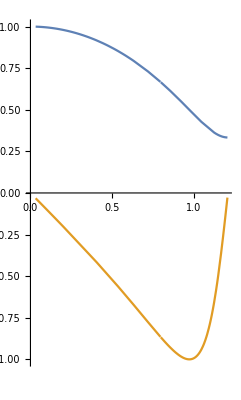

```mathematica
(* Derivation t[ρ]; all correct, but not interpretable much *)

ClearAll["Global`*"]
Clear["Global`*"]
$Pre=.(*clear the prior definition for $Pre*)
echo=Function[main, Unevaluated[main]/.Set -> Function[, Print@HoldForm[#=#2]; #=#2, HoldFirst], HoldAll];

$Assumptions := {{ρ[t], φ, GM, t[y], y[ρ], ρ0, ω0, u[t], δ, C1, C2, C3} ∈ Reals, t > 0, ρ[t] > 0, ρ0 > 0}

(* Radial component equation without derive *)
eq1 := ρ''[t] == ρ[t] ω[t]^2 - GM/ρ[t]^2
(* Tangential component solution without derive *)
ω[t_] = T0 / ρ[t]^2; //echo
T0s = ω0 ρ0^2; //echo

(* u[t]  := (ρ')[t] *)
eq2 =  eq1 /. {ρ''[t] ->u ⅆu/ⅆρ, ρ[t] -> ρ}
uu[u_] = eq2⟦1⟧ ⅆρ/ⅆu;
ρρ[ρ_] = eq2⟦2⟧ ⅆρ/ⅆρ;
eq21 =∫uu[u]ⅆu == ∫ρρ[ρ]ⅆρ + C1; //echo

ρ[0] := ρ0
sol = Solve[eq21 /. {u->0, ρ->ρ0}, C1]
C1s = sol⟦1,1,2⟧;

u[ρ_] = δ * u /. Solve[eq21, u]⟦1⟧;
eq3 = t'[ρ] == 1/u[ρ]; //echo

y[ρ_] = ρ + GM/(2 C1); //echo
sol = Solve[y[ρ] == y, ρ];
repl = sol⟦1,1⟧;

C2s = (2 GM^2)/C1 + 4 T0^2; //echo
eq4 = Simplify[Simplify[eq3 /. {t'[ρ]->t'[y], repl}], C2s == C2]; //echo

sol4 = DSolve[eq4, t[y], y]; //echo
t[y_] = Simplify[sol4⟦1,1,2⟧] /. {C[1]->C3};
t[ρ_] = t[y[ρ]]; //echo

sol5 = Solve[t[ρ0] == 0, C3]; //echo
C3s = sol5⟦1,1,2⟧;

t[ρ_] = Simplify[{t[ρ], δ=1, ω0=1, ρ0=1, GM=2, T0=T0s, C1=C1s, C2=C2s, C3=C3s}]⟦1⟧; //echo
ParametricPlot[{{t[ρ], ρ},{t[ρ], 1/t'[ρ]}}, {ρ, 0, 3}]
```

{{ρ[t],ρ,φ,φ[ρ],t[y],y[ρ],u[t],z[y]}∈ℝ,t>0,ρ[t]>0,ρ0>0,ω0>0,y>0,{GM,T0,ρ0,ω0,C1,C2s,C3,C4,δ}∈{Constants,ℝ},C4∈{Constants,ℝ},δ∈{Constants,ℝ}}

ω[t_]=T0/ρ[t]^2

T0s=ρ0^2 ω0

(u ⅆu)/ⅆρ==T0^2/ρ^3-GM/ρ^2

eq21=u^2/2==C1-T0^2/(2 ρ^2)+GM/ρ

{{C1→(T0^2-2 GM ρ0)/(2 ρ0^2)}}

t'[ρ]=-ρ/(δ √(-T0^2+2 GM ρ+2 C1 ρ^2))

ω[ρ]=T0/ρ^2

eq4=φ'[ρ]==-T0/(δ ρ √(-T0^2+2 GM ρ+2 C1 ρ^2))

y[ρ_]=1/ρ

repl41=ρ→1/y

dyy=-y^2

eq41=φ'[y]==T0/(√(2 C1+2 GM y-T0^2 y^2) δ)

z[y_]=-GM+T0^2 y

repl42=y→(GM+z)/T0^2

dzz=T0^2

eq42=φ'[z]==1/(√(GM^2+2 C1 T0^2-z^2) δ)

C2s=GM^2+2 C1 T0^2

eq43=φ'[z]==1/(√(C2-z^2) δ)

z3[z_]=z/(√C2)

repl43=z→√C2 z3

dz3z3=1/(√C2)

eq44=φ'[z3]==1/(√(1-z3^2) δ)

sol4={{φ[z3]→C4+ArcSin[z3]/δ}}

subs4=φ[ρ]→C4+ArcSin[(-GM+T0^2/ρ)/(√C2)]/δ

φ[ρ_]=C4+ArcSin[(-GM+T0^2/ρ)/(√C2)]/δ

C4s=-ArcSin[(-GM+T0^2/ρ0)/(√C2)]/δ

δ=-1

ω0=1

ρ0=1

GM=2

T0=1

C1=-3/2

C2=1

C4=-π/2

φ[ρ_]=-π/2+ArcSin[2-1/ρ]

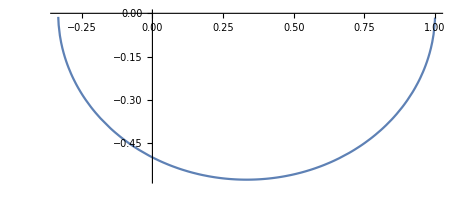

```mathematica
(* Derivation ρ[ω] *)

ClearAll["Global`*"]
Clear["Global`*"]
$Pre=.(*clear the prior definition for $Pre*)
echo=Function[main, Unevaluated[main]/.Set -> Function[, Print@HoldForm[#=#2]; #=#2, HoldFirst], HoldAll];

$Assumptions = {
{ρ[t], ρ, φ, φ[ρ], t[y], y[ρ], u[t], z[y]} ∈ ℝ,
t > 0, ρ[t] > 0, ρ0 > 0, ω0 > 0, y > 0, 
{GM, T0, ρ0, ω0, C1, C2s, C3, C4, δ} ∈ {Constants, ℝ}, C4 ∈ {Constants, ℝ}, δ ∈ {Constants, ℝ}
}

(* Radial component equation without derive *)
eq1 := ρ''[t] == ρ[t] ω[t]^2 - GM/ρ[t]^2
(* Tangential component solution without derive *)
ω[t_] = T0 / ρ[t]^2; //echo
T0s = ω0 ρ0^2; //echo

(* u[t]  := (ρ')[t] *)
eq2 =  eq1 /. {ρ''[t] ->u ⅆu/ⅆρ, ρ[t] -> ρ}
uu[u_] = eq2⟦1⟧ ⅆρ/ⅆu;
ρρ[ρ_] = eq2⟦2⟧ ⅆρ/ⅆρ;
eq21 =∫uu[u]ⅆu == ∫ρρ[ρ]ⅆρ + C1; //echo

ρ[0] := ρ0
sol = Solve[eq21 /. {u->0, ρ->ρ0}, C1]
C1s = sol⟦1,1,2⟧;

u[ρ_] = δ * u /. Solve[eq21, u]⟦1⟧;
t'[ρ] = 1/u[ρ]; //echo

ω[ρ] = ω[t] /. {ρ[t]-> ρ}; //echo
(*  ω = ⅆφ/ⅆt = (ⅆφ ⅆρ)/(dρ ⅆt) = φ'[ρ]/t'[ρ] *)

eq4 = φ'[ρ] == ω[ρ] t'[ρ]; //echo

y[ρ_] = 1/ρ ; //echo
repl41 = Solve[y[ρ] == y, ρ]⟦1,1⟧; //echo
dyy = y'[ρ] /. repl41; //echo
eq41 = Simplify[eq4 /. {φ'[ρ]->φ'[y] dyy, repl41}]; //echo

z[y_] =  y T0^2 - GM; //echo
repl42 = Solve[z[y] == z, y]⟦1,1⟧; //echo
dzz = z'[y] /. repl42; //echo
eq42 = Simplify[eq41 /. {φ'[y]->φ'[z] dzz, repl42}, T0 > 0]; //echo

C2s = GM^2+2 C1 T0^2 ; //echo
eq43 = Simplify[eq42, C2 == C2s]; //echo

z3[z_] =  z /√C2; //echo
repl43 = Solve[z3[z] == z3, z]⟦1,1⟧; //echo
dz3z3 = z3'[z] /. repl43; //echo
eq44 = Simplify[eq43 /. {φ'[z]->φ'[z3] dz3z3, repl43}, C2 > 0]; //echo
sol4 = DSolve[eq44, φ[z3], z3] /. {C[1] -> C4}; //echo

subs4 = sol4⟦1,1⟧ /. {φ[z3] -> φ[ρ], z3 -> z3[z[y[ρ]]]}; //echo
φ[ρ_] = φ[ρ] /. subs4; //echo

C4s = Solve[φ[ρ0] == 0, C4]⟦1,1,2⟧; //echo
φ[ρ_] = Simplify[{φ[ρ], δ=-1, ω0=1, ρ0=1, GM=2, T0=T0s, C1=C1s, C2=C2s, C4 = C4s}]⟦1⟧; //echo
ParametricPlot[{ρ Cos[φ[ρ]], ρ Sin[φ[ρ]]}, {ρ, 0, 7}]
```